# Basic MadEvent Analysis Routines

by David Curtin (david.r.curtin@gmail.com)
based on Chameleon Package by Jessie Thaler, Natalia Toro and Philip Schuster, 2005 (http://v1.jthaler.net/olympics/software.html)

## Saving & Loading non-LHS/LHCO files

```mathematica
SaveIt[filename_, expr_]:=Module[{output},
output=Export[filename<>".dat", ToString[expr//InputForm], "String"];
ClearMemory;
output
];

SaveIt[varnamestring_]:=Module[{output},
output=Export[varnamestring<>".dat", ToString[ToExpression[varnamestring]//InputForm], "String"];
ClearMemory;
output
];

ReadIt[filename_]:=Module[{output},
output=ToExpression[Import[StringReplace[filename,".dat"->""]<>".dat", "String"]];
ClearMemory;
output
];


(*crop the image after exporting it*)
ExportCrop[path_,toimage_, borderpixels_]:=Module[{},
Export[path,toimage];
fiximage = Import[path];
imagedim =ImageDimensions[fiximage];
fixedimage = ImageCrop[ImageTake[fiximage,{0,imagedim[[2]]-borderpixels},{4,imagedim[[1]]-borderpixels}]];
Export[path,fixedimage]
];


(*crop the image after exporting it*)
ExportCrop[path_,toimage_, borderpixels1_,borderpixels2_]:=Module[{},
Export[path,toimage];
fiximage = Import[path];
imagedim =ImageDimensions[fiximage];
fixedimage = ImageCrop[ImageTake[fiximage,{0,imagedim[[2]]-borderpixels1},{4,imagedim[[1]]-borderpixels2}]];
Export[path,fixedimage]
];



Arrange1Din2Dgrid[list1D_,wanteddimensions_]:=Table[Join[list1D, Table["",{wanteddimensions[[1]]wanteddimensions[[2]]-Length[list1D]}]][[col+(row-1)(wanteddimensions[[2]])]],{row,1,wanteddimensions[[1]]},{col,1,wanteddimensions[[2]]}];

ImageDumpCrop[x_]:=ExportCrop["E:\\Documents\\uni\\Research\\SUSY gaugino mass project\\mathematica notebooks\\Calculations for our own GKK model\\image.png",x,5];

ImageDump[x_]:=Export["E:\\Documents\\uni\\Research\\SUSY gaugino mass project\\mathematica notebooks\\Calculations for our own GKK model\\image.png",x];




ImageDumpCrop[filename_,x_]:=ExportCrop["E:\\Documents\\uni\\Research\\SUSY gaugino mass project\\mathematica notebooks\\Calculations for our own GKK model\\imagesSU1\\"<>filename<>".png",x,3];
ImageDumpCrop[filename_,x_, borderpixels_]:=ExportCrop["E:\\Documents\\uni\\Research\\SUSY gaugino mass project\\mathematica notebooks\\Calculations for our own GKK model\\imagesSU1\\"<>filename<>".png",x,borderpixels];
ImageDump[filename_,x_]:=Export["E:\\Documents\\uni\\Research\\SUSY gaugino mass project\\mathematica notebooks\\Calculations for our own GKK model\\imagesSU1\\"<>filename<>".png",x];

(*I think this might help with the memory bloat*)
ClearMemory:=Module[{},
Unprotect[In,Out];
Clear[In,Out];
Protect[In,Out];
ClearSystemCache[];
];
```

## Read Events [MGME LHE, pythia LHE, PGS]

read MGME LHE events

```mathematica
(*quick way to read the events... put all that stuff into a function*)
(*ReadEvents[filename_]:=Module[{eventListp, eventListOutLp, Nev},
Print["Time taken to read events: ",Timing[testp=Import[filename,"Table"];][[1]]];
Timing[eventListp=ReadME[testp]; ]; (*convert raw data into chameleon-readable form*)
Nev = Length[eventListp]-1;
eventListOutLp=SetOut[eventListp]; (*remove initial particle info -- boring for e+e- collider*)
{eventListp, eventListOutLp, Nev}
]
*)
(*new version of this function: discards dummy empty entry at end of eventslist*)
ReadEvents[filename_]:=Module[{eventListp, eventListOutLp,Nevents,xsection},
Print["Time taken to read events: ",Timing[testp=Import[filename,"Table"];][[1]]];
Timing[eventListp=ReadME[testp]; ]; 
(*convert raw data into chameleon-readable form*)
(*eventListp = eventListp[[1;;(Length[eventListp]-1)]];*)
(*drop dummy event at end*)
eventListOutLp=SetOut[eventListp]; (*remove initial particle info -- boring for e+e- collider*)
MGGIpos=Position[testp,{"<MGGenerationInfo>"}]⟦1,1⟧;
{Nevents,xsection}={testp⟦MGGIpos+1,6⟧,testp⟦MGGIpos+2,6⟧};
(*extract number of events and cross section in pb*)
ClearMemory;
{eventListp, eventListOutLp,Nevents,xsection}
];




ReadME[rawInput_ ] := 
(
(*Search for beginning of events*)
pos=Position[rawInput,{"</init>"}][[1,1]]; 
(*Throw away crap at start of file, combine events in {} array and remove the XML commands and compulsory eventinfo *)
DeleteCases[Split[Drop[ rawInput, pos],#=!={"</event>"}&],{_}|{_,_}|{_,_,_}|{_,_,_,_}| eventInfo,2]
);
```

read pythia LHE events

```mathematica
ReadEventsPythia[filename_]:=Module[{eventListp, eventListOutLp},
Print["Time taken to read events: ",Timing[testp=Import[filename,"Table"];][[1]]];
Timing[eventListp=ReadMEPythia[testp]; ]; 
(*convert raw data into chameleon-readable form*)
eventListp = eventListp[[1;;(Length[eventListp]-1)]];
(*drop dummy event at end*)
eventListOutLp=SetOut[eventListp]; (*remove initial particle info -- boring for e+e- collider*)
ClearMemory;
{eventListp, eventListOutLp}
];




ReadMEPythia[rawInput_ ] := 
(
(*Search for beginning of events*)
pos=Position[rawInput,{"<event>"}][[1,1]]; 
(*Throw away crap at start of file, combine events in {} array and remove the XML commands and compulsory eventinfo *)
pythiaout=DeleteCases[Split[Drop[ rawInput, pos],#=!={"</event>"}&],{"<event>"}|{"</LesHouchesEvents>"}| {"</event>"} | eventInfo,2];
ClearMemory;
pythiaout
);
```

Reading PGS events into the same format we use for MGME events

The below code is also used in the automatic .m scripts to convert lots of lhe/lhco files to .dat files

```mathematica
(*give this function the filename of a PGS output file and it gives you an eventlist in the same format as MGME output*)
ReadPGSEventsAsMGME[filename_]:=ReadPGSEventFile[filename]//ConvertPGSeventstoMGMEevents;
```

```mathematica
(*give this function the filename of the PGS output file and it'll give you a list of events. Use PGSEventPrint to show a single event*)
ReadPGSEventFile[filename_]:=Module[{SplitData,PGSreadfile,found,entry,entryTableHeading,numevents,PGSeventlist},

SplitData[rawObjList_]:=Split[Drop[rawObjList,If[NumberQ[rawObjList[[1,1]]],0,1]],Less[First[#1],First[#2]]&];

PGSreadfile=SplitData[Import[filename,"Table"]];



(*find the entry in the read tabel where the table starts, i.e. table header. After that it's normal PGS events.*)
found=False;
entry = 0;
While[found==False&&entry<  Length[PGSreadfile],
entry++;
If[PGSreadfile[[entry]]=={{"#","typ","eta","phi","pt","jmas","ntrk","btag","had/em","dum1","dum2"}},
found=True;];
];
If[entry ≥  Length[PGSreadfile], entry=0];
entryTableHeading = entry;

(*get total number of events*)
numevents = Length[PGSreadfile]-entryTableHeading;
(*store list of PGS events*)
PGSeventlist = Table[Drop[PGSreadfile[[entryTableHeading+eventindex]],1],{eventindex,1,numevents}];
ClearMemory;
PGSeventlist
];



PGSEventPrint[PGSevent_]:=Join[{{"#","typ","eta","phi","pt","jmas","ntrk","btag","had/em","dum1","dum2"}}, PGSevent]//MatrixForm//Print;
```

```mathematica
(*give this function a list of PGS events that have been read by ReadPGSEventFile and it outputs a list of events that is in the same format as the MGME events*)
ConvertPGSeventstoMGMEevents[PGSevents_]:=Module[{output}, 
output = Table[PGSevents[[eventindex]][[particleindex]]//ConvertPGSparticletoMGMEparticle,{eventindex,1,Length[PGSevents]},{particleindex,1,Length[PGSevents[[eventindex]]]}];
ClearMemory[];
output
];

(*use these pointers to access entries of a single PGS event*)
typePGSINDEX = 2;
etaPGSINDEX = 3;
phiPGSINDEX = 4;
ptPGSINDEX = 5;
jmasPGSINDEX = 6;
ntrkPGSINDEX=7;
btagPGSINDEX=8;


ConvertPGSparticletoMGMEparticle[PGSparticle_]:=Module[{currenttype,currenteta,currentphi,currentpt,currentjmas,currentntrk,currentbtag,currentpx,currentpy,currenttheta,currentpz,currentPID},
(*load parameters of this particle into *)
currenttype = PGSparticle[[typePGSINDEX]];
currenteta = PGSparticle[[etaPGSINDEX]];
currentphi = PGSparticle[[phiPGSINDEX]];
currentpt = PGSparticle[[ptPGSINDEX]];
currentjmas = PGSparticle[[jmasPGSINDEX]];
currentntrk = PGSparticle[[ntrkPGSINDEX]];
currentbtag=PGSparticle[[btagPGSINDEX]];



currentpx = currentpt Cos[currentphi];
currentpy = currentpt Sin[currentphi];

currenttheta = 2 ArcTan[Exp[-currenteta]];

currentpz = currentpt/Tan[currenttheta];


(*note we are discarding some τ information here -- namely, whether it decayed via three prongs (ntrk = ± 3) or one prong (ntrk = ± 1)*)
(*we are also discarding whether the tagged b was tight (btag = 2) or loose (btag = 1)*)
Which[
(*photon*)
currenttype==0, currentPID = 22,
(*e+*)
currenttype==1&&currentntrk==1, currentPID = -11,
(*e-*)
currenttype==1&&currentntrk==-1, currentPID = 11,
(*μ+*)
currenttype==2&&currentntrk==1, currentPID = -13,
(*μ-*)
currenttype==2&&currentntrk==-1, currentPID = 13,
(*τ+*)
currenttype==3&&currentntrk>0, currentPID = -15,
(*τ-*)
currenttype==3&&currentntrk<0, currentPID = 15,
(*b*)
currenttype==4&&currentbtag>0, currentPID = 5,
(*other jet: label as gluon*)
currenttype ==4 && currentbtag==0, currentPID= 21,
(*MET: label as electron-neutrino*)
currenttype==6, currentPID = 12
];


{currentPID,1,0,0,0,0,currentpx,currentpy,currentpz,√(currentpx^2+currentpy^2+currentpz^2),currentjmas,0,0}
];
```

```mathematica
ReadPGSEventFileAsMGME[filename_]:=Module[{temp},
temp=ReadPGSEventFile[filename];
ConvertPGSparticletoMGMEparticle[temp]
];
```

## EventPrint

```mathematica
(*MAKE SURE TO UPDATE THIS IF YOU HAVE A NEW INVISIBLE PARTICLE*)
invisiblelist={12,-12,14,-14,16,-16,1000022}
```

{12,-12,14,-14,16,-16,1000022}

```mathematica
(* Based on the Chameleon package by Philip Shuster, Jesse Thaler, Natalia Toro *)
(* Modified by Maxim Perelstein and Andi Weiler, 2008-09 *)

(*format of the compulsory event vector*)
eventInfo={_,_,_,_,_,_};

ClearAll[particle,finout];

(*PDG numbers see e.g. http://home.fnal.gov/~maeshima/alignment/ORCA/PYTHIA_particle_codes.ps*)

{2,-2,1,-1,3,-3,4,-4,5,-5,6,-6,21};


PIDu= 2;
PIDubar = -2;
PIDd = 1;
PIDdbar = -1;
PIDs = 3;
PIDsbar = -3;
PIDc = 4;
PIDcbar = -4;
PIDb = 5;
PIDbbar = -5;
PIDt = 6;
PIDtbar = -6;
PIDeminus = 11;
PIDeplus = -11;
PIDnue=12;
PIDnuebar = -12;
PIDmuminus = 13;
PIDmuplus =-13;
PIDnumu = 14;
PIDnumubar = -14;
PIDtauminus = 15;
PIDtauplus = -15;
PIDnutau = 16;
PIDnutaubar = -16;
PIDgluon = 21;
PIDphoton = 22;
PIDZ = 23;
PIDWplus = 24;
PIDWminus = -24;
PIDh = 25;

particle[2] ="u";
particle[-2] ="uBar";

particle[1] ="d";
particle[-1] ="dBar";

particle[3] ="s";
particle[-3] ="sBar";

particle[4] ="c";
particle[-4] ="cBar";

particle[5] ="b";
particle[-5] ="bBar";

particle[6] ="t";
particle[-6] ="tBar";

particle[11] ="e^-";
particle[-11] ="e^+";

particle[12] ="⋁_e ";
particle[-12] ="(⋁_e)^c";

particle[13] ="μ^-";
particle[-13]="μ^+";

particle[14] ="⋁_μ ";
particle[-14] ="(⋁_μ)^c";


particle[15] ="τ^-";
particle[-15]="τ^+";

particle[16] ="⋁_τ ";
particle[-16] ="(⋁_τ)^c";




particle[21] ="gluon";
particle[22] = "γ";
particle[23] = "Z";
particle[24] ="W^+";
particle[-24] = "W^-";

particle[1000006] ="(t̃)_1";
particle[-1000006] ="((t̃)_1)^*";
particle[1000022] ="((χ̃)_1)^0";
particle[1000021] = "g̃";
particle[1000005]="(b̃)_1";
particle[-1000005]="(b̃)_1*";

particle[2000001]="OverTilde[d_R]";
particle[-2000001]="OverTilde[d_R]*";

particle[2000002]="OverTilde[u_R]";
particle[-2000002]="OverTilde[u_R]*";


particle[25] = "h";

(*for exotic higgs decay analysis using Prerit's  omdel*)
particle[45] = "a";
particle[46] = "a'";


finout[-1] = "in";
finout[1] = "out";
finout[2]  = "decayed";


EventPrint[event_]:=Which[
Length[event[[1]]] == 13, 
EventPrintNoTag[event], 
Length[event[[1]]] == 14,
EventPrintTag[event],
Length[event[[1]]] ==15,
EventPrintRecon[event],
Length[event[[1]]]==16,
EventPrintComb[event],
Length[event[[1]]]==17,
EventPrintMCRecon[event]
];

ClearAll[x1,x2];

EventPrintNoTag[ event_ ] := Module[{printevent, numlist, x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13, x14,x15,x16,x17,x18,x19},
printevent = Join[{{pid, in/out,mother1,mother2,color1,color2, px,py,pz,p0,mass,6,hel}}, (event/.{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_}->{particle[x1],finout[x2],x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13})];
numlist =Join[{"#"}, Table[i,{i,1,Length[event]}]];
Print[Join[{numlist},Transpose[printevent]]//Transpose//MatrixForm];
]; 

EventPrintTag[ event_ ] := Module[{printevent, numlist, x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13, x14,x15,x16,x17,x18,x19},
printevent = Join[{{pid, in/out,mother1,mother2,color1,color2, px,py,pz,p0,mass,6,hel, "tag"}}, (event/.{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_, x14_}->{particle[x1],finout[x2],x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,tagname[x14]})];
numlist =Join[{"#"}, Table[i,{i,1,Length[event]}]];
Print[Join[{numlist},Transpose[printevent]]//Transpose//MatrixForm];
]; 


EventPrintRecon[ event_ ] := Module[{printevent, numlist, x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13, x14,x15,x16,x17,x18,x19},
printevent = Join[{{pid, in/out,mother1,mother2,color1,color2, px,py,pz,p0,mass,6,hel, "tag", "recon"}}, (event/.{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_, x14_,x15_}->{particle[x1],finout[x2],x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,tagname[x14],x15})];
numlist =Join[{"#"}, Table[i,{i,1,Length[event]}]];
Print[Join[{numlist},Transpose[printevent]]//Transpose//MatrixForm];
]; 

EventPrintComb[ event_ ] := Module[{printevent, numlist, x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13, x14,x15,x16,x17,x18,x19},
printevent = Join[{{pid, in/out,mother1,mother2,color1,color2, px,py,pz,p0,mass,6,hel, "tag", "recon", "comb"}}, (event/.{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_, x14_,x15_,x16_}->{particle[x1],finout[x2],x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,tagname[x14],x15,x16})];
numlist =Join[{"#"}, Table[i,{i,1,Length[event]}]];
Print[Join[{numlist},Transpose[printevent]]//Transpose//MatrixForm];
]; 


EventPrintMCRecon[ event_ ] := Module[{printevent, numlist, x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13, x14,x15,x16,x17,x18,x19},
printevent = Join[{{pid, in/out,mother1,mother2,color1,color2, px,py,pz,p0,mass,6,hel, "tag", "recon", "comb", "MCrecon"}}, (event/.{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_, x14_,x15_,x16_, x17_}->{particle[x1],finout[x2],x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,tagname[x14],x15,x16, x17})];
numlist =Join[{"#"}, Table[i,{i,1,Length[event]}]];
Print[Join[{numlist},Transpose[printevent]]//Transpose//MatrixForm];
];
```

## Histograming

### basic 1D histograms

```mathematica
RescaledHistogram[data_, xsecmultiplier_,binspec_,options___]:=Module[{bla},
bla=HistogramList[data,binspec];
ListPlot[Transpose[{Drop[bla[[1]],-1],xsecmultiplier bla[[2]]}],Joined->True,InterpolationOrder->0, options]
];


RescaledLogHistogram[data_, xsecmultiplier_,binspec_,options___]:=Module[{bla},
bla=HistogramList[data,binspec];
ListLogPlot[Transpose[{Drop[bla[[1]],-1],xsecmultiplier bla[[2]]}],Joined->True,InterpolationOrder->0, options]
];



RescaledLogHistogramWithError[data_, xsecmultiplier_,binspec_,options___]:=Module[{bla,upbla,downbla},
bla=HistogramList[data,binspec];
bla=Transpose[{Drop[bla[[1]],-1], bla[[2]]}];
upbla={#[[1]],#[[2]]+Max[1,√(#[[2]])]}&/@bla;
downbla={#[[1]],10^-12+ #[[2]]-√(#[[2]])}&/@bla;
Show[
ListLogPlot[Join[Evaluate[{#[[1]],xsecmultiplier/10#[[2]]}&/@#&/@{bla}],Evaluate[{#[[1]],2 xsecmultiplier #[[2]]}&/@#&/@{bla}]],Joined->True,InterpolationOrder->0, PlotStyle->None, options]
,
ListLogPlot[Evaluate[{#[[1]],xsecmultiplier#[[2]]}&/@#&/@{bla}],Joined->True,InterpolationOrder->0, options]
,
ListLogPlot[Evaluate[{#[[1]],xsecmultiplier#[[2]]}&/@#&/@{ upbla, downbla}],Joined->True,InterpolationOrder->0, PlotStyle->None, Filling->{1->{{2},Directive[Gray,Opacity[0.3]]}}]
]
];


RescaledHistogramWithError[data_, xsecmultiplier_,binspec_,options___]:=Module[{bla,upbla,downbla},
bla=HistogramList[data,binspec];
bla=Transpose[{Drop[bla[[1]],-1], bla[[2]]}];
upbla={#[[1]],#[[2]]+Max[1,√(#[[2]])]}&/@bla;
downbla={#[[1]],#[[2]]-√(#[[2]])}&/@bla;

Show[
ListPlot[Evaluate[{#[[1]],xsecmultiplier#[[2]]}&/@#&/@{bla}],Joined->True,InterpolationOrder->0, options]
,
ListPlot[Evaluate[{#[[1]],xsecmultiplier#[[2]]}&/@#&/@{ upbla, downbla}],Joined->True,InterpolationOrder->0, PlotStyle->None, Filling->{1->{{2},Directive[Gray,Opacity[0.3]]}}]
]
];




RescaledHistogramWithErrorLogAndLinear[data_, xsecmultiplier_,binspec_,options___]:={{
RescaledHistogramWithError[data, xsecmultiplier,binspec,options], RescaledLogHistogramWithError[data, xsecmultiplier,binspec,options]}}//TableForm;
```

### 2D heatmaps

```mathematica
Make2DHistogramsNoStatCheck[data_,histrange1_,histrange2_, dataname_, {xname_,yname_}]:=Module[{binstartpoints1,binstartpoints2, datalist, numdatapointslist, output},

{binstartpoints1,binstartpoints2, datalist, numdatapointslist}=WeightedHistogramList[data,histrange1,histrange2];
plotlistSAVE = Flatten[Table[{binstartpoints1[[i]]+histrange1[[3]]/2,binstartpoints2[[j]]+histrange2[[3]]/2,datalist[[i]][[j]]},{i,1,Dimensions[datalist][[1]]},{j,1,Dimensions[datalist][[2]]}],1];


output =ListDensityPlot[
plotlistSAVE,
PlotRange->All,FrameLabel->{xname, yname}, ImageSize->500, PlotRange->All,ColorFunction->"SolarColors", BaseStyle->{FontWeight->Normal,FontSize->15}, PlotLabel->dataname, InterpolationOrder->0]//TableForm;

ClearMemory[];

output
];


Make2DHistograms[data_,histrange1_,histrange2_, dataname_, {xname_,yname_}]:=Module[{binstartpoints1,binstartpoints2, datalist, numdatapointslist, output},

{binstartpoints1,binstartpoints2, datalist, numdatapointslist}=WeightedHistogramList[data,histrange1,histrange2];
plotlistSAVE = Flatten[Table[{binstartpoints1[[i]]+histrange1[[3]]/2,binstartpoints2[[j]]+histrange2[[3]]/2,datalist[[i]][[j]]},{i,1,Dimensions[datalist][[1]]},{j,1,Dimensions[datalist][[2]]}],1];

plotliststatSAVE = Flatten[Table[{binstartpoints1[[i]]+histrange1[[3]]/2,binstartpoints2[[j]]+histrange2[[3]]/2,numdatapointslist[[i]][[j]]},{i,1,Dimensions[datalist][[1]]},{j,1,Dimensions[datalist][[2]]}],1];

output = {{ListDensityPlot[
plotlistSAVE,
PlotRange->All,FrameLabel->{xname, yname}, ImageSize->500, PlotRange->All,ColorFunction->"SolarColors", BaseStyle->{FontWeight->Normal,FontSize->15}, PlotLabel->dataname, InterpolationOrder->0],
ListDensityPlot[
plotliststatSAVE,
PlotRange->All,FrameLabel->{xname, yname}, ImageSize->500, PlotRange->All,ColorFunction->"SolarColors", BaseStyle->{FontWeight->Normal,FontSize->15}, PlotLabel->"statistics check [ignoring weight]", InterpolationOrder->0]}}//TableForm;

ClearMemory[];

output
];
```

```mathematica
(*input: a list of entries like (weight, {data1, data2})*)
(*output: *)
WeightedHistogramList[data_, {startrange1_, endrange1_, binwidth1_}, {startrange2_, endrange2_, binwidth2_}] := Module[{binstartpoints1, binstartpoints2, datalist, numdatapointslist, currentweight, currentdata, bin1, bin2},
  
  binstartpoints1 = Drop[Table[i, {i, startrange1, endrange1, binwidth1}], -1];
  binstartpoints2 = Drop[Table[i, {i, startrange2, endrange2, binwidth2}], -1];
  datalist = Table[0, {Length[binstartpoints1]}, {Length[binstartpoints2]}]; (*this will be the data to make the weighted histogram*)
  numdatapointslist = datalist; (*this contains the number of weighted datapoints that went into each bin*)
  
  Monitor[
   Do[
     currentweight = data[[dataindex]][[1]];
     currentdata = data[[dataindex]][[2]];
     
     bin1 = -1;
     bin2 = -1;
     
     Do[
       If[IsInRange[currentdata[[1]], binstartpoints1[[i]] + {0, binwidth1}],
         bin1 = i;
         i = Length[binstartpoints1] + 10; (*exit loop*)
         ];
       ,
       {i, 1, Length[binstartpoints1]}]
      
      Do[
       If[IsInRange[currentdata[[2]], binstartpoints2[[i]] + {0, binwidth2}],
         bin2 = i;
         i = Length[binstartpoints2] + 10; (*exit loop*)
         ];
       ,
       {i, 1, Length[binstartpoints2]}];
     
     If[bin1 > 0 && bin2 > 0,
      datalist[[bin1]][[bin2]] = datalist[[bin1]][[bin2]] + currentweight;
      numdatapointslist[[bin1]][[bin2]]++;
      ];
     
     
     
     , {dataindex, 1, Length[data]}];
   , dataindex];
  
  ClearMemory;
  
  {binstartpoints1, binstartpoints2, datalist, numdatapointslist}
  
  
  ]
```

## Accessing basic kinematic properties of an event entry (i.e. a PARTICLE)

Note
etaOf has been updated to be PSEUDORAPIDITY, and rapOf is now the real rapidity (previously called etaOf)

```mathematica
(* those are input or decayed particles*)
decayedOrIn = {_,-1,_,_,_,_,_,_,_,_,_,_,_}  | {_,2,_,_,_,_,_,_,_,_,_,_,_};

EventOut[ event_ ]  := (DeleteCases[event,decayedOrIn]);

SetOut[ event_ ]  := (DeleteCases[event,decayedOrIn,2]);

(* EffMassAll[objList_]  :=Plus @@ Map[ptOf,objList//Transpose,{2}]; *)

EffMass[event_]  :=Plus @@ Map[ptOf,event,{1}];

pT[event_]  :=Map[ptOf,event,{1}]//Flatten;
eta[event_] := Map[etaOf,event,{1}]//Flatten;
theta[event_] := Map[thetaOf,event,{1}]//Flatten;
threeVector[event_] := Map[ThreeVectorFrom,event,{1}];


MissingEnergy[event_] := Plus @@ Map[enOf,event,{1}];


ptOf[{_,_,_,_,_,_,px_,py_,___}]:=√(px^2+py^2);
ptVec[{_,_,_,_,_,_,px_,py_,___}]:={px,py};

enOf[{_,_,_,_,_,_,_,_,_,En_,___}]:=En;
thetaOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:= ArcCos[pz/√(px^2 + py^2+ pz^2)];


(*we want to follow fastjet convention and return phi in the range (0, 2π) *)

phifn[px_,py_]:=Which[
px > 0 && py > 0, 
ArcTan[py/px]
, 
px < 0 && py > 0,
ArcTan[py/px] + π
,
px < 0 && py < 0,
π+ ArcTan[py/px]
,
px > 0 && py < 0, 
2π + ArcTan[py/px]

]

phiOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:= phifn[px,py];
AbsMin[list_]:=Sort[list,Abs[#1]<Abs[#2]&]⟦1⟧;

(*
DeltaR[part1_,part2_]:=√((etaOf[part1] - etaOf[part2])^2 +
 Min[{
(phiOf[part1]-phiOf[part2])^2
,
(2 π - (phiOf[part1]-phiOf[part2]))^2
,
(2 π + (phiOf[part1]-phiOf[part2]))^2
}]);
*)


DeltaR[part1_,part2_]:=√((etaOf[part1] - etaOf[part2])^2 +
 DeltaPhi[part1,part2]^2);



DeltaPhi[part1_,part2_]:=AbsMin[{
(phiOf[part1]-phiOf[part2])
,
(2 π - (phiOf[part1]-phiOf[part2]))
,
(2 π + (phiOf[part1]-phiOf[part2]))
}];

(*

(*these are wrong! I don't know where the hell they came from...*)
etaOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:=- Log[ Abs[Tan[ ArcCos[pz/√(px^2 + py^2+ pz^2)]/2]]]; 

etaOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:= ArcSinh[pz/√(px^2 + py^2)];

*)

(*this is actual rapidity!!*)
rapOf[{_,_,_,_,_,_,px_,py_,pz_,e_,___}]:=1/2 Log[(e+pz)/(e-pz)];
(*this is pseudorapidity*)
etaOf[{_,_,_,_,_,_,px_,py_,pz_,e_,___}]:=-Log[Tan[ArcCos[pz/√(px^2 + py^2+ pz^2)]/2]];



FourVectorFrom[{_,_,_,_,_,_,px_,py_,pz_,En_,___}] := {En, px, py,pz };

(*FourLength[{pe_,pz_,px_,py_}] := Sqrt[Max[pe^2 - pz^2 - px^2 - py^2,0.0]];*)

FourLength[{pe_,pz_,px_,py_}] := Sqrt[pe^2 - pz^2 - px^2 - py^2];

FourLengthSq[{pe_,pz_,px_,py_}] := pe^2 - pz^2 - px^2 - py^2;

ThreeVectorFrom[{_,_,_,_,_,_,px_,py_,pz_,___}] := { px, py,pz };

CosthetaTwoJet[{jet1_,jet2_}] := Module[{a,b},a = ThreeVectorFrom[jet1]; b=  ThreeVectorFrom[jet2]; a.b/√(a.a b.b)];

GetAll[evt_]:=evt;
all[evt_]:=True;

Freq[evtList_,crit_,objsel_,plotfunc_,{min_,max_,nbins_}]:=BinCounts[ Flatten[ plotfunc/@Flatten4[objsel/@Select[evtList,crit]]],{min,max,(max-min)/nbins}];

Flatten4[List_]:=Flatten[List,Max[0,Depth[List]-4]];

HGet[patt_,All][evt_]:=Cases[evt,patt];

oJetlhe=  {2,1,_,_,_,_,_,_,_,_,_,_,_}  | {-2,1,_,_,_,_,_,_,_,_,_,_,_}|{21,1,_,_,_,_,_,_,_,_,_,_,_}  ;

oMissingEnergy = {8888,1,_,_,_,_,_,_,_,_,_,_,_}  ;

PTSort[event_]:=Sort[event,Greater[ptOf[#1],ptOf[#2]]&];


and[f_][evt_]:=f[evt];
and[f_,g__][evt_]:=f[evt]&&and[g][evt];
or[f_][evt_]:=f[evt];
or[f_,g__][evt_]:=f[evt]||or[g][evt];

join[f_][evt_]:=f[evt];
join[f_,g__][evt_]:=Join[f[evt],join[g[evt]]];
```

## More useful kinematic functions & observables

```mathematica
Wmass = 80.4;
tmass = 174.3;
Zmass = 91.2;

MGMEwmass = 79.82;
MGMEtmass = 175;

FourDotProduct[v_,u_]:=v[[1]] u[[1]] - v[[2;;4]].u[[2;;4]];


(*finds the smallest entry of a list of real numbers and returns {min, positin of min in list}
*)
FindMin[list_]:=Module[{currentmin, currentminPosn, i},
currentmin = Infinity;
currentminPosn = 0;
For[i = 1, i≤Length[list],i++,
If[list[[i]]<currentmin, currentminPosn = i; currentmin = list[[i]]];
];
{currentmin, currentminPosn}
];

(*if anything in number, range is imaginary, return FALSE!*)
IsInRange[number_,range_]:=If[number range[[1]] range[[2]]  ∈ Reals, TrueQ[(number ≥ range[[1]])&&(number ≤range[[2]])], False, False];


InvMassSq[event_,particleList_]:= FourLength[ Sum[FourVectorFrom[event[[particleList[[i]]]]],{i,1,Length[particleList]}]]^2;

(*invariant mass with jet rescaling, used e.g. in top reconstruction*)
InvMassScaled[event_,particleList_,scalelist_]:= FourLength[ Sum[scalelist[[i]]FourVectorFrom[event[[particleList[[i]]]]],{i,1,Length[particleList]}]];


InvMass[event_,particleList_]:= FourLength[ Sum[FourVectorFrom[event[[particleList[[i]]]]],{i,1,Length[particleList]}]];


InvMass[particles_]:= FourLength[ Sum[FourVectorFrom[particles[[i]]],{i,1,Length[particles]}]];


(*creates a list with entries {xi, "number of events between xi -dx and xi + dx"} -- basically a histogram in listplot form, more useful for some applications}*)
MyBinList[list_, {xmin_,xmax_, dx_}]:={Table[xmin - dx/2 + i dx,{i,1,IntegerPart[(xmax-xmin)/dx]}],BinCounts[list, {xmin, xmax, dx}]}//Transpose;

(*just like my regular MyBinList function, except the counts are renormalized by a set number*)
MyRenormalizedBinList[list_, {xmin_,xmax_, dx_}, norm_]:={Table[xmin - dx/2 + i dx,{i,1,IntegerPart[(xmax-xmin)/dx]}],norm BinCounts[list, {xmin, xmax, dx}]}//Transpose;


(*that way I don't have to memorize where in each event[[particle]] entry the various variables are*)
{pidIndex , inoutIndex,mother1Index ,mother2Index,color1Index, color2Index, pxIndex, pyIndex, pzIndex, p0Index, massIndex, sixIndex, helIndex, tagindex, reconindex, combindex, MCreconindex} = {1,2,3,4,5,6,7,8,9,10,11,12,13, 14,15, 16, 17};


(*Feed this function a list of {True,False,True,True,...} and it'll return True IFF all entries are TRUE*)
AllTrue[booleanlist_]:=If[Length[Union[booleanlist]]==1, (Union[booleanlist][[1]]),False];


VectorLength[vec_]:=√(vec.vec);

(*finds total visible pT (vector) from an OUT-event*)
TotalVisiblepT[event_]:=Module[{visiblept, currentparticle, i},
visiblept = {0,0};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[!MemberQ[invisiblelist, currentparticle[[pidIndex]]],
visiblept =  {currentparticle[[pxIndex]],currentparticle[[pyIndex]]} + visiblept;
];
];
visiblept
];

(*finds total visible pT (vector) from an OUT-event*)
TotalVisiblep[event_]:=Module[{visiblept, currentparticle, i},
visiblept = {0,0,0};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[!MemberQ[invisiblelist, currentparticle[[pidIndex]]],
visiblept =  {currentparticle[[pxIndex]],currentparticle[[pyIndex]],currentparticle[[pzIndex]]} + visiblept;
];
];
visiblept
];


missingpT[event_]:=-TotalVisiblepT[event];
missingET[event_]:=-TotalVisiblepT[event];

MET[event_] := missingET[event];


HT[particles_]:=Sum[particles[[i]]//ptOf,{i,1,Length[particles]}];



(*all of the below functions with names like xxxxJetpTxxx take an event and a list of PIDs or TAGs and return either the maximum pT of those particles, or a list of all pTs (vector lengths) or a list of pTs (vectors)*)


(*this function reconstructs neutrino transverse momentum (assuming there's only one!) to get the total transverse mass for a given event*)
(*assumes Subscript[M, T]^2 = (∑ |Subscript[p, T]|)^2 - (∑ Subscript[p, T])^2  =  (∑ Subscript[E, T])^2 - (∑ Subscript[p, T])^2   *)
TotalMT[event_]:=Module[{visiblepts, currentevent, i, neutrinopt, allpt,MT},
(*collect all the visible pts*)
visiblepts ={};
For[i = 1, i≤Length[event],i++,
currentevent = event[[i]];
If[!MemberQ[invisiblelist, currentevent[[pidIndex]]],
visiblepts = Append[visiblepts,  {currentevent[[pxIndex]],currentevent[[pyIndex]]} ]
];
];
(*reconstruct neutrino pT*)
neutrinopt = -Sum[visiblepts[[i]],{i,1,Length[visiblepts]}];
allpt = Append[visiblepts, neutrinopt];
MT = √(Sum[VectorLength[allpt[[i]]],{i,1,Length[allpt]}]^2 - VectorLength[Sum[allpt[[i]],{i,1,Length[allpt]}]]^2);
MT
];




(*takes all possible jet pairs (by PID) and gives the minimum DeltaR jet seperation *)
MinDeltaRJetsPID[event_]:= Module[{alljets,alljetpairs,ΔRlist},
alljets = FindParticles[event, jetlist];
alljetpairs = Subsets[alljets,{2}];
ΔRlist = Table[DeltaR[event[[alljetpairs[[i]][[1]]]],event[[alljetpairs[[i]][[2]]]]],{i,1,Length[alljetpairs]}];
Min[ΔRlist]
];

(*takes all possible jet pairs (by TAG) and gives the minimum DeltaR jet seperation *)
MinDeltaRJetsTAG[event_]:= Module[{alljets,alljetpairs,ΔRlist},
alljets = FindTags[event, {btag, jettag}];
alljetpairs = Subsets[alljets,{2}];
ΔRlist = Table[DeltaR[event[[alljetpairs[[i]][[1]]]],event[[alljetpairs[[i]][[2]]]]],{i,1,Length[alljetpairs]}];
Min[ΔRlist]
];
```

SetDelayed::write: Tag AllTrue in AllTrue[booleanlist_] is Protected.

## Finding particle entries in an event

```mathematica
(*feed this function an event and a list of particle IDs and it'll output a list of indices indicating which particles in the event are of that type*)
FindParticles[event_,pidlist_]:=Module[{indexlist ,i,j},
indexlist = {};
For[i = 1, i≤Length[event],i++,
For[j = 1, j≤Length[pidlist],j++,
If[event[[i]][[pidIndex]] == pidlist[[j]], indexlist = Append[indexlist, i]]; Break;
];
];
indexlist
];

FindTags[event_,taglist_]:=Module[{indexlist ,i,j},
indexlist = {};
For[i = 1, i≤Length[event],i++,
For[j = 1, j≤Length[taglist],j++,
If[event[[i]][[tagindex]] == taglist[[j]], indexlist = Append[indexlist, i]]; Break;
];
];
indexlist
];


FindRecon[event_,reconlist_]:=Module[{indexlist ,i,j},
indexlist = {};
For[i = 1, i≤Length[event],i++,
For[j = 1, j≤Length[reconlist],j++,
If[event[[i]][[reconindex]] == reconlist[[j]], indexlist = Append[indexlist, i]]; Break;
];
];
indexlist
];

FindMCRecon[event_,reconlist_]:=Module[{indexlist ,i,j},
indexlist = {};
For[i = 1, i≤Length[event],i++,
For[j = 1, j≤Length[reconlist],j++,
If[event[[i]][[MCreconindex]] == reconlist[[j]], indexlist = Append[indexlist, i]]; Break;
];
];
indexlist
];
```

## Finding sets of particles based on their pT-ranking in a list

```mathematica
(*finds pT of most energetic jet using exact particle IDs*)
jetPIDlist = {2,-2,1,-1,3,-3,4,-4,5,-5,6,-6,21};

(*obsolete naming*)
jetlist = jetPIDlist;

μPIDlist = {-13,13};
ePIDlist = {-11,11};
τPIDlist = {15,-15};
leptonPIDlist = Join[μPIDlist,ePIDlist,τPIDlist];
lightleptonPIDlist = Join[μPIDlist,ePIDlist];
bPIDlist = {5,-5};


HighestJetpT[event_] := HighestJetpT[event,jetlist];

(*as above, except we can specify the jetlist*)
HighestJetpT[event_, jetlist_]:=Module[{jetpts, currentparticle, i},
jetpts = {};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[MemberQ[jetlist, currentparticle[[pidIndex]]],
jetpts = Append[jetpts, VectorLength[{currentparticle[[pxIndex]],currentparticle[[pyIndex]]}]];
];
];
Max[jetpts]
];

SmallestJetpT[event_, jetlist_]:=Module[{jetpts, currentparticle, i},
jetpts = {};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[MemberQ[jetlist, currentparticle[[pidIndex]]],
jetpts = Append[jetpts, VectorLength[{currentparticle[[pxIndex]],currentparticle[[pyIndex]]}]];
];
];
Min[jetpts]
];

AllJetpTVec[event_, jetlist_]:=Module[{jetpts, currentparticle, i},
jetpts = {};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[MemberQ[jetlist, currentparticle[[pidIndex]]],
jetpts = Append[jetpts, {currentparticle[[pxIndex]],currentparticle[[pyIndex]]}];
];
];
jetpts
];

AllJetpT[event_, jetlist_]:=Module[{jetpts, currentparticle, i},
jetpts = {};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[MemberQ[jetlist, currentparticle[[pidIndex]]],
jetpts = Append[jetpts, VectorLength[{currentparticle[[pxIndex]],currentparticle[[pyIndex]]}]];
];
];
jetpts
];


(*finds pT of most energetic jet (b or regular) using TAGS*)
(*ONLY INPUT A TAGGED EVENT*)
HighestJetpTTags[event_]:=Module[{jetpts, currentparticle, i},
jetpts = {};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[MemberQ[{btag, jettag}, currentparticle[[tagindex]]],
jetpts = Append[jetpts, VectorLength[{currentparticle[[pxIndex]],currentparticle[[pyIndex]]}]];
];
];
Max[jetpts]
];


(*finds pT of most energetic jet (b or regular) using TAGS*)
(*ONLY INPUT A TAGGED EVENT*)
AllJetpTTags[event_, taglist_]:=Module[{jetpts, currentparticle, i},
jetpts = {};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[MemberQ[taglist, currentparticle[[tagindex]]],
jetpts = Append[jetpts, VectorLength[{currentparticle[[pxIndex]],currentparticle[[pyIndex]]}]];
];
];
jetpts
];

AllJetpTTags[event_] := AllJetpTTags[event,{btag, jettag}];
```

```mathematica
(*outputs the number of particles specified by the PIDlist that have pT > minpT*)
NumberJetsWithpTAbovepTMin[currentevent_,PIDlist_,minpT_]:=Module[{temp,temp2,temp3},
temp=AllJetpT[currentevent,jetlist];
temp2 = temp-minpT//Sign;
temp3 = 0 temp2 + 1;
Sum[(temp3[[i]]+temp2[[i]])/2,{i,1,Length[temp3]}]
];
```

## Example: 14 TeV pp Collision at LHC

We run a 14 TeV proton proton collisions at the LHC and obtain an output in an LHE file. This is done using the command 

	crmc -x -o lhe -n1 -m0 -S14000 -f ~/allMyStuff/BoostedDM/crmcruns/14TeVpp.lhe

This generates a Les Housches Event file in the location shown. In terms of the other options;
	
	-x  		print cross section to terminal
	-o lhe  	output format is lhe
	-n1  		100 collisions
	-m0  		EPOS_LHC event model
	-S14000  	s^(1/2)=14000 GeV=14 TeV
	-f /path/  	choice of output file

We can now try to begin analysing the .lhe  file using the functions above.

```mathematica
LHEfile="/mnt/james/lhe/14000.00-1.lhe";
Print["Time taken to read events: ", Timing[testp=Import[LHEfile, "Table"];][[1]]];
eventList=ReadME[testp];
Print["Number of events: ", Nevents=Length[eventList]];
```

Time taken to read events: 0.

Number of events: 1

```mathematica
EventPrint[eventList[[1]]]
```

(# | pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
1 | particle[2212] | finout[-9] | -1 | -1 | 0 | 0 | 0. | 0. | 14000. | 14000. | 0.93828 | 6.96465×10^17 | 9.
2 | particle[2212] | finout[-9] | -1 | -1 | 0 | 0 | 0. | 0. | 6.35107×10^-8 | 0.93828 | 0.93828 | 2.49074×10^19 | 9.
3 | particle[211] | out | 1 | 2 | 0 | 0 | -0.169446 | 0.21645 | 4172.92 | 4172.92 | 0.13957 | 1.10661×10^8 | 9.
4 | particle[111] | decayed | 1 | 2 | 0 | 0 | -0.106592 | -0.163031 | 101.917 | 101.917 | 0.134977 | 0.00433694 | 9.
5 | particle[2112] | out | 1 | 2 | 0 | 0 | 0.220505 | -0.407447 | 2.41372 | 2.63124 | 0.93957 | 3.88987×10^14 | 9.
6 | particle[211] | out | 1 | 2 | 0 | 0 | -0.170269 | 0.300878 | 1.08696 | 1.14913 | 0.13957 | 56914.8 | 9.
7 | particle[111] | decayed | 1 | 2 | 0 | 0 | -0.160572 | 0.183635 | 0.611731 | 0.672264 | 0.134977 | 0.000281306 | 9.
8 | particle[21214] | decayed | 1 | 2 | 0 | 0 | 0.218589 | -0.209109 | 4.24622 | 4.58618 | 1.70622 | 2.2586×10^-12 | 9.
9 | particle[-211] | out | 1 | 2 | 0 | 0 | 0.513712 | -0.0192182 | 36.6341 | 36.638 | 0.13957 | 4.00268×10^6 | 9.
10 | particle[311] | decayed | 1 | 2 | 0 | 0 | -0.459949 | -0.422887 | 63.664 | 63.669 | 0.49767 | 6.12293×10^-9 | 9.
11 | particle[211] | out | 1 | 2 | 0 | 0 | 0.173635 | -0.525727 | 11.7906 | 11.8045 | 0.13957 | 365177. | 9.
12 | particle[221] | decayed | 1 | 2 | 0 | 0 | -1.11448 | 0.504591 | 7.85417 | 7.96774 | 0.547853 | 1.12141×10^-6 | 9.
13 | particle[113] | decayed | 1 | 2 | 0 | 0 | -0.509257 | -0.174995 | 14.1501 | 14.1816 | 0.77549 | 9.09761×10^-13 | 9.
14 | particle[213] | decayed | 1 | 2 | 0 | 0 | 0.0691785 | 0.164006 | 43.281 | 43.2883 | 0.77549 | 1.00568×10^-11 | 9.
15 | particle[-211] | out | 1 | 2 | 0 | 0 | 0.0680837 | -0.236216 | 46.9082 | 46.909 | 0.13957 | 3.38629×10^6 | 9.
16 | particle[213] | decayed | 1 | 2 | 0 | 0 | -0.114101 | -0.0522783 | 53.6137 | 53.6195 | 0.77549 | 1.03283×10^-11 | 9.
17 | particle[211] | out | 1 | 2 | 0 | 0 | 0.0489046 | 0.153283 | 585.573 | 585.573 | 0.13957 | 2.53005×10^7 | 9.
18 | particle[113] | decayed | 1 | 2 | 0 | 0 | 0.0441891 | 0.0233465 | 3089.49 | 3089.49 | 0.77549 | 6.6923×10^-9 | 9.
19 | particle[111] | decayed | 1 | 2 | 0 | 0 | -0.321966 | -0.100659 | 407.5 | 407.5 | 0.134977 | 0.0189643 | 9.
20 | particle[113] | decayed | 1 | 2 | 0 | 0 | 0.477058 | 0.146862 | 119.938 | 119.941 | 0.77549 | 5.63729×10^-10 | 9.
21 | particle[113] | decayed | 1 | 2 | 0 | 0 | 0.852276 | 0.239061 | 83.4044 | 83.4127 | 0.77549 | 3.53473×10^-11 | 9.
22 | particle[111] | decayed | 1 | 2 | 0 | 0 | -0.139096 | -0.12869 | 10.266 | 10.2686 | 0.134977 | 0.000509615 | 9.
23 | particle[-1114] | decayed | 1 | 2 | 0 | 0 | 1.30732 | 0.0925189 | 142.736 | 142.747 | 1.232 | 3.23707×10^-11 | 9.
24 | particle[111] | decayed | 1 | 2 | 0 | 0 | 0.217188 | 0.0182184 | 455.566 | 455.566 | 0.134977 | 0.0700637 | 9.
25 | particle[-213] | decayed | 1 | 2 | 0 | 0 | -0.193198 | -0.102295 | 675.406 | 675.407 | 0.77549 | 3.5105×10^-11 | 9.
26 | particle[3112] | out | 1 | 2 | 0 | 0 | 0.771841 | -0.454416 | 2583.3 | 2583.3 | 1.1974 | 60757.3 | 9.
27 | particle[311] | decayed | 1 | 2 | 0 | 0 | -0.683024 | -0.100085 | 73.0962 | 73.1011 | 0.49767 | 1.91043×10^-8 | 9.
28 | particle[321] | out | 1 | 2 | 0 | 0 | -0.505681 | 0.27772 | 479.232 | 479.232 | 0.493677 | 2.46615×10^6 | 9.
29 | particle[-311] | decayed | 1 | 2 | 0 | 0 | 0.322968 | 0.131932 | 110.959 | 110.96 | 0.49767 | 6.27168×10^-9 | 9.
30 | particle[-213] | decayed | 1 | 2 | 0 | 0 | 0.122402 | -0.0871827 | 70.2209 | 70.2253 | 0.77549 | 3.98672×10^-11 | 9.
31 | particle[-311] | decayed | 1 | 2 | 0 | 0 | -0.754246 | 0.896528 | 30.1933 | 30.2201 | 0.49767 | 5.80226×10^-9 | 9.
32 | particle[111] | decayed | 1 | 2 | 0 | 0 | -0.499383 | 0.0939094 | 19.2925 | 19.2997 | 0.134977 | 0.00226353 | 9.
33 | particle[111] | decayed | 1 | 2 | 0 | 0 | -0.300386 | -0.064433 | 58.4771 | 58.4781 | 0.134977 | 0.00462435 | 9.
34 | particle[-213] | decayed | 1 | 2 | 0 | 0 | 0.341154 | -0.0501476 | 216.131 | 216.133 | 0.77549 | 1.13077×10^-10 | 9.
35 | particle[211] | out | 1 | 2 | 0 | 0 | 0.173496 | -0.000877544 | 103.722 | 103.723 | 0.13957 | 1.58084×10^6 | 9.
36 | particle[-211] | out | 1 | 2 | 0 | 0 | 0.259154 | -0.143246 | 126.573 | 126.574 | 0.13957 | 2.89788×10^6 | 9.
37 | γ | out | 4 | 0 | 0 | 0 | -0.0429224 | 0.0157129 | 24.772 | 24.7721 | 0. | 2.40041×10^18 | 9.
38 | γ | out | 4 | 0 | 0 | 0 | -0.0636701 | -0.178744 | 77.1448 | 77.1451 | 0. | 3.7673×10^19 | 9.
39 | γ | out | 7 | 0 | 0 | 0 | -0.157987 | 0.1508 | 0.597898 | 0.636539 | 0. | 8.49889×10^18 | 9.
40 | γ | out | 7 | 0 | 0 | 0 | -0.00258435 | 0.0328358 | 0.0138327 | 0.0357242 | 0. | 5.46603×10^18 | 9.
41 | particle[1114] | decayed | 8 | 0 | 0 | 0 | -0.186041 | -0.00128239 | 3.29234 | 3.52022 | 1.232 | 1.469×10^-12 | 9.
42 | particle[211] | out | 8 | 0 | 0 | 0 | 0.40463 | -0.207826 | 0.953879 | 1.06597 | 0.13957 | 8699.93 | 9.
43 | particle[130] | out | 10 | 0 | 0 | 0 | -0.459949 | -0.422887 | 63.661 | 63.666 | 0.497614 | 1.23779×10^6 | 9.
44 | γ | out | 12 | 0 | 0 | 0 | -1.03568 | 0.240488 | 6.38989 | 6.47775 | 0. | 7.18495×10^18 | 9.
45 | γ | out | 12 | 0 | 0 | 0 | -0.0788007 | 0.264103 | 1.46428 | 1.48999 | 0. | 2.89193×10^18 | 9.
46 | particle[211] | out | 13 | 0 | 0 | 0 | 0.0240964 | -0.113275 | 0.815353 | 0.83528 | 0.13957 | 1648.01 | 9.
47 | particle[-211] | out | 13 | 0 | 0 | 0 | -0.533353 | -0.0617206 | 13.3348 | 13.3463 | 0.13957 | 19069.7 | 9.
48 | particle[211] | out | 14 | 0 | 0 | 0 | 0.104437 | 0.152803 | 41.816 | 41.8167 | 0.13957 | 17147.1 | 9.
49 | particle[111] | decayed | 14 | 0 | 0 | 0 | -0.0352589 | 0.0112029 | 1.46491 | 1.47158 | 0.134977 | 0.000726342 | 9.
50 | particle[211] | out | 16 | 0 | 0 | 0 | 0.171776 | 0.242083 | 30.1046 | 30.1064 | 0.13957 | 2.79209×10^6 | 9.
51 | particle[111] | decayed | 16 | 0 | 0 | 0 | -0.285877 | -0.294361 | 23.5091 | 23.5131 | 0.134977 | 0.000153586 | 9.
52 | particle[211] | out | 18 | 0 | 0 | 0 | 0.306619 | -0.130875 | 2277.59 | 2277.59 | 0.13957 | 3.17013×10^7 | 9.
53 | particle[-211] | out | 18 | 0 | 0 | 0 | -0.26243 | 0.154222 | 811.906 | 811.906 | 0.13957 | 2.56904×10^7 | 9.
54 | γ | out | 19 | 0 | 0 | 0 | -0.201489 | -0.0387304 | 309.97 | 309.97 | 0. | 1.48113×10^19 | 9.
55 | γ | out | 19 | 0 | 0 | 0 | -0.120477 | -0.0619291 | 97.5307 | 97.5308 | 0. | 1.06495×10^19 | 9.
56 | particle[211] | out | 20 | 0 | 0 | 0 | 0.467333 | 0.382617 | 68.1203 | 68.1231 | 0.13957 | 834331. | 9.
57 | particle[-211] | out | 20 | 0 | 0 | 0 | 0.00972506 | -0.235755 | 51.8176 | 51.8184 | 0.13957 | 1.77928×10^6 | 9.
58 | particle[211] | out | 21 | 0 | 0 | 0 | 0.487773 | -0.152988 | 24.6375 | 24.6432 | 0.13957 | 1.31193×10^6 | 9.
59 | particle[-211] | out | 21 | 0 | 0 | 0 | 0.364504 | 0.392049 | 58.7669 | 58.7695 | 0.13957 | 6.36067×10^6 | 9.
60 | γ | out | 22 | 0 | 0 | 0 | 0.0163565 | -0.0586004 | 2.25035 | 2.25117 | 0. | 8.94157×10^18 | 9.
61 | γ | out | 22 | 0 | 0 | 0 | -0.155453 | -0.0700899 | 8.01562 | 8.01744 | 0. | 1.05551×10^19 | 9.
62 | particle[-2112] | out | 23 | 0 | 0 | 0 | 1.01313 | 0.141907 | 128.581 | 128.589 | 0.93957 | 5.24737×10^16 | 9.
63 | particle[211] | out | 23 | 0 | 0 | 0 | 0.294189 | -0.0493879 | 14.1543 | 14.1581 | 0.13957 | 308860. | 9.
64 | γ | out | 24 | 0 | 0 | 0 | 0.111218 | -0.0203689 | 120.227 | 120.227 | 0. | 4.37615×10^18 | 9.
65 | γ | out | 24 | 0 | 0 | 0 | 0.10597 | 0.0385873 | 335.34 | 335.34 | 0. | 3.45389×10^17 | 9.
66 | particle[-211] | out | 25 | 0 | 0 | 0 | -0.0474297 | -0.124472 | 41.4444 | 41.4449 | 0.13957 | 256623. | 9.
67 | particle[111] | decayed | 25 | 0 | 0 | 0 | -0.145768 | 0.0221775 | 633.962 | 633.962 | 0.134977 | 0.248962 | 9.
68 | particle[310] | out | 27 | 0 | 0 | 0 | -0.683024 | -0.100085 | 73.0934 | 73.0983 | 0.497614 | 3963.26 | 9.
69 | particle[310] | out | 29 | 0 | 0 | 0 | 0.322968 | 0.131932 | 110.956 | 110.957 | 0.497614 | 10471.8 | 9.
70 | particle[-211] | out | 30 | 0 | 0 | 0 | 0.029053 | 0.320316 | 31.2856 | 31.2876 | 0.13957 | 314619. | 9.
71 | particle[111] | decayed | 30 | 0 | 0 | 0 | 0.0933489 | -0.407498 | 38.9353 | 38.9377 | 0.134977 | 0.000604792 | 9.
72 | particle[310] | out | 31 | 0 | 0 | 0 | -0.754246 | 0.896528 | 30.1923 | 30.2191 | 0.497614 | 2383.28 | 9.
73 | γ | out | 32 | 0 | 0 | 0 | -0.270219 | 0.0955142 | 8.81947 | 8.82413 | 0. | 1.15147×10^18 | 9.
74 | γ | out | 32 | 0 | 0 | 0 | -0.229164 | -0.00160481 | 10.4731 | 10.4756 | 0. | 1.25114×10^19 | 9.
75 | γ | out | 33 | 0 | 0 | 0 | -0.0690508 | -0.0598029 | 10.2256 | 10.226 | 0. | 7.53117×10^18 | 9.
76 | γ | out | 33 | 0 | 0 | 0 | -0.231335 | -0.00463012 | 48.2516 | 48.2521 | 0. | 7.47521×10^18 | 9.
77 | particle[-211] | out | 34 | 0 | 0 | 0 | 0.406749 | 0.124205 | 193.072 | 193.073 | 0.13957 | 2.88302×10^6 | 9.
78 | particle[111] | decayed | 34 | 0 | 0 | 0 | -0.0655949 | -0.174352 | 23.0591 | 23.0603 | 0.134977 | 0.00338329 | 9.
79 | particle[2112] | out | 41 | 0 | 0 | 0 | -0.161957 | 0.218524 | 2.44321 | 2.63174 | 0.93957 | 4.82162×10^13 | 9.
80 | particle[-211] | out | 41 | 0 | 0 | 0 | -0.024084 | -0.219806 | 0.849125 | 0.888475 | 0.13957 | 110772. | 9.
81 | γ | out | 49 | 0 | 0 | 0 | 0.0208465 | 0.0247383 | 1.20089 | 1.20133 | 0. | 4.62811×10^18 | 9.
82 | γ | out | 49 | 0 | 0 | 0 | -0.0561054 | -0.0135354 | 0.264019 | 0.270254 | 0. | 1.99×10^18 | 9.
83 | γ | out | 51 | 0 | 0 | 0 | -0.0951433 | -0.130443 | 12.7864 | 12.7874 | 0. | 1.56545×10^19 | 9.
84 | γ | out | 51 | 0 | 0 | 0 | -0.190733 | -0.163918 | 10.7227 | 10.7256 | 0. | 3.03052×10^18 | 9.
85 | γ | out | 67 | 0 | 0 | 0 | -0.00363249 | -0.0302735 | 246.63 | 246.63 | 0. | 5.83595×10^18 | 9.
86 | γ | out | 67 | 0 | 0 | 0 | -0.142135 | 0.052451 | 387.332 | 387.332 | 0. | 2.10547×10^18 | 9.
87 | γ | out | 71 | 0 | 0 | 0 | 0.111602 | -0.390663 | 37.912 | 37.9142 | 0. | 2.74821×10^18 | 9.
88 | γ | out | 71 | 0 | 0 | 0 | -0.0182531 | -0.016835 | 1.02326 | 1.02356 | 0. | 1.05285×10^19 | 9.
89 | γ | out | 78 | 0 | 0 | 0 | -0.0619384 | -0.02006 | 10.4527 | 10.4529 | 0. | 1.75397×10^19 | 9.
90 | γ | out | 78 | 0 | 0 | 0 | -0.00365648 | -0.154292 | 12.6064 | 12.6074 | 0. | 5.99222×10^18 | 9.)

We can obtain the total cross section by running the crmc code with an -x flag. Then, the cross section σ(pp → π^0+...) can be found by multiplying by the ratio of number of π^0 produced and the total number of particles.

```mathematica
FindParticles[eventList[[1]], particle[111]]
```

{4,7,19,22,24,32,33,49,51,67,71,78}

```mathematica
nπ0 = Sum[Length[FindParticles[eventList[[i]], particle[111]]],{i, 1, Nevents}];
σ=79.95; (*mb*)
σppπ0 = σ nπ0 / Nevents * 10^9; (*pb*)
Print["σ(pp -> π^0) = ", σppπ0, " pb"]
```

σ(pp -> π^0) = 9.594×10^11 pb

Then we can use the result from Feng et al. (1708.09389) to compute the σ(pp → χχ) cross section as a function of the vector mediator mass m_A'.

σ(pp→ χχ)=2(ϵ^2(1-(m_A'/(m_(π^0)))^2))^3 B(π^0→ γγ)σ(pp→ π^0)
Assuming the branching ratio of π^0 to γγ is approximately 100%, we then see the following plot;

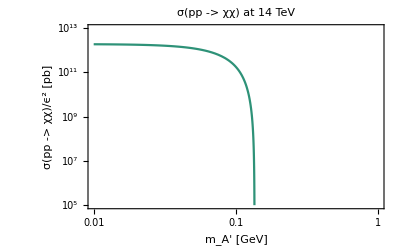

```mathematica
mπ=0.135; (* GeV *)
σppχχ[mA_]:= 2 (1 - mA^2/mπ^2)^3 σppπ0; (* ϵ^-2 pb *)
LogLogPlot[σppχχ[mA], {mA, 10^-2, mπ},Frame->True, PlotRange->{{10^-2,10^0}, {10^5,10^13}},FrameLabel->{"m_A' [GeV]","σ(pp -> χχ)/ϵ^2 [pb]"},LabelStyle->FontSize->16,PlotLabel->"σ(pp -> χχ) at 14 TeV", PlotStyle -> {RGBColor["#2E9278"]}]
```

-Graphics-